```mathematica
(* =================================================================*)
(* 1. PARÁMETROS DEL SISTEMA *)
(* =================================================================*)

ClearAll["Global`*"]

(*Parámetros magnéticos*)
gamma=2.8; (*Proporción giromagnética en MHz/Oe*)
H0=770.0;(*Campo magnético aplicado en Oe*)
Ms=1750.0;(*Magnetización de saturación en Gauss*)
deltaH=0.5;(*Ancho de línea FMR en Oe*)

(*Frecuencias angulares en rad/ns (GHz*2Pi) para consistencia de unidades*)
wH=2*Pi*(gamma*H0/1000.0);
wM=2*Pi*(gamma*Ms/1000.0);

(*Parámetros geométricos en micrómetros (um)*)
dPF=8.3;(*Espesor de la película plana*)
delta=1.0;(*Profundidad del surco*)
dG=dPF-delta;(*Espesor en el surco*)

LPF=330.0;(*Longitud de la región plana*)
LG=70.0;(*Longitud del surco*)
Nperiods=12;   (*Número de surcos (períodos)*)
```

```mathematica
(* =================================================================*)
(*2. VECTORES DE ONDA Y ATENUACIÓN ESPACIAL*)
(* =================================================================*)

(*Vector de onda real k(w,d) en rad/um*)
kWave[w_,d_]:=-(1/(2*d))*Log[1+(4/wM^2)*(wH*(wH+wM)-w^2)]

(*Velocidad de grupo vg(w,d) en um/ns*)
vg[w_,d_]:=(wM^2*d*Exp[-2*kWave[w,d]*d])/(4*w)

(*Factor de atenuación espacial k'(w,d) en rad/um*)
(*deltaH*gamma está en MHz,multiplicamos por 2Pi*10^-3 para rad/ns*)
kPrime[w_,d_]:=(2*Pi*(gamma*deltaH/1000.0))/Abs[vg[w,d]]
```

```mathematica
(* =================================================================*)
(*3. MATRICES DE LÍNEA DE TRANSMISIÓN*)
(* =================================================================*)

(*Coeficiente de reflexión por salto de impedancia geométrica*)
GammaRef=delta/(2*dPF-delta);

(*Matriz de propagación para una región genérica*)
Tprop[w_,d_,L_]:=Module[{k=kWave[w,d],kp=kPrime[w,d]},{{Exp[-(I*k-kp)*L],0},{0,Exp[(I*k-kp)*L]}}]

(*Matrices de interfaz en los bordes del surco*)
Tinterface[nu_]:=(1/(1-GammaRef))*{{1,nu*GammaRef},{nu*GammaRef,1}}

(*Matriz total de la Celda Unidad*)
Tcell[w_]:=Tprop[w,dPF,LPF].Tinterface[1].Tprop[w,dG,LG].Tinterface[-1]

(*Matriz completa del Cristal Magnónico (N períodos)*)
TMC[w_]:=MatrixPower[Tcell[w],Nperiods]
```

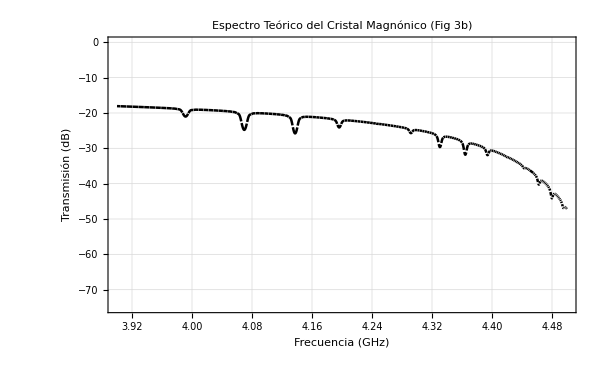

```mathematica
(* =================================================================*)
(*4. CÁLCULO DE TRANSMISIÓN Y GRÁFICA*)
(* =================================================================*)

(*Potencia transmitida Pw=1/ |T_11|^2*)
TransmissionPower[fGHz_]:=Module[{w,Ttotal,T11},w=2*Pi*fGHz;
Ttotal=TMC[w];
T11=Ttotal[[1,1]];
1/(Abs[T11]^2)]

(*Límite inferior de frecuencia (Resonancia Ferromagnética)*)
fMin=Sqrt[wH*(wH+wM)]/(2*Pi)+0.02;

(*Gráfica del espectro de transmisión en dB vs Frecuencia (GHz)*)
Plot[10*Log10[TransmissionPower[f]],{f,3.9,4.5},PlotRange->{{3.9,4.5},{-75,0}},PlotPoints->300,MaxRecursion->3,Frame->True,FrameLabel->{"Frecuencia (GHz)","Transmisión (dB)"},PlotLabel->"Espectro Teórico del Cristal Magnónico (Fig 3b)",FrameStyle->Directive[Black,12],PlotStyle->Directive[Black,Thickness[0.003]],GridLines->Automatic, ImageSize->600]
```

```mathematica
(* =================================================================*)
(*1. PARÁMETROS GEOMÉTRICOS Y MATRICES *)
(* =================================================================*)

Lambda=LPF+LG; (*Constante de red en um (400 um)*)

(*Matriz de interfaz exacta según Ec.5 *)
Tinterface[nu_]:=(1/(1-nu*GammaRef))*{{1,nu*GammaRef},{nu*GammaRef,1}}

(*Matriz de la celda unidad (1 período)*)
Tcell[w_]:=Tprop[w,dPF,LPF].Tinterface[1].Tprop[w,dG,LG].Tinterface[-1]

(* =================================================================*)
(*2. CÁLCULO DEL VECTOR DE ONDA DE BLOCH*)
(* =================================================================*)

(*Vector de onda K en rad/cm*)
KBloch[fGHz_]:=Module[{w,tr,K_um},w=2*Pi*fGHz;
tr=Tr[Tcell[w]];
K_um=Re[ArcCos[tr/2]/Lambda];
K_um*10000]
```